# Homework 2

## Derek Prince APPM 2450 - 002, Fall 2015 Due 4 September, 2015

```mathematica
Clear["Global`*"];
```

## Problem 1

A.

Particle 1: x_1= 2cos(t)  y_1= 2sin(t) 0 ≤ t ≤ 2π
Particle 2: x_2 = 3cost(t)  y_2 = -1 + sin(t) 0 ≤ t ≤ 2π

```mathematica
r1[t_]={2Cos[t],2Sin[t]}; (* particle 1 *)
r2[t_]={3Cos[t],-1+Sin[t]}; (* particle 2 *)
```

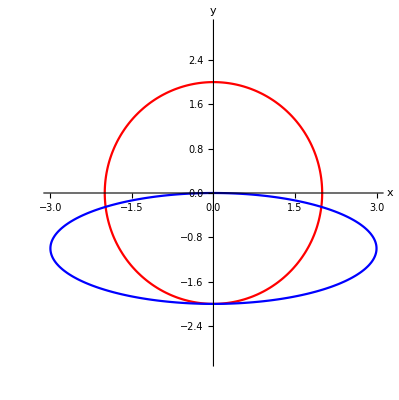

```mathematica
particle1 = ParametricPlot[Style[r1[t], Red], {t, 0, 2π}];
particle2 = ParametricPlot[Style[r2[t],Blue], {t, 0, 2π}];
Show[{particle1, particle2}, 
PlotRange -> {-3,3}, AxesLabel-> {Style["x", Bold, Medium], Style["y", Bold, Medium]}] (* Aspect Ratio doesn't like working with both functions at once - thus  *)
```

#### B.

```mathematica
intersect1 = FindRoot[r1[t]==r2[s],{t,1},{s,1}];
intersect2=FindRoot[r1[t]==r2[s],{t,3},{s,3}];
```